```mathematica
ρ1j=0.2;
ρ2j=0.2;
v10=50;
v20=50;
v1e[ρ1_,ρ2_]:=v10((1+ⅇ^((ρ1/ρ1j-0.25)/0.06))^-1-3.72 10^-6)(1-(ρ1+ρ2)/(ρ1j+ρ2j))
v2e[ρ1_,ρ2_]:=v20((1+ⅇ^((ρ2/ρ2j-0.25)/0.06))^-1-3.72 10^-6)(1-(ρ1+ρ2)/(ρ1j+ρ2j))
```

```mathematica
(*ρ1j=0.15;
ρ2j=0.2;
v10=40;
v20=30;
v1e[ρ1_,ρ2_]:=v10*(1-ρ1/ρ1j)(1-((ρ1+ρ2)/(ρ1j+ρ2j))^2)
v2e[ρ1_,ρ2_]:=v20*(1-ρ2/ρ2j)(1-((ρ1+ρ2)/(ρ1j+ρ2j))^2)*)
```

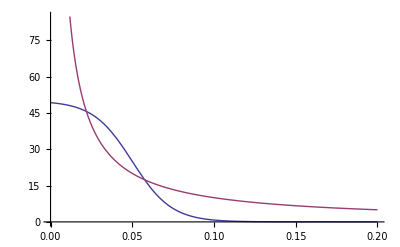

```mathematica
Plot[{v10((1+ⅇ^((ρ1/ρj-0.25)/0.06))^-1-3.72 10^-6),1/ρ1},{ρ1,0,ρ1j}]
```

```mathematica
Plot3D[ρ1*v1e[ρ1,ρ2]+v2e[ρ1,ρ2]*ρ2,{ρ1,0,ρ1j},{ρ2,0,ρ2j},AxesLabel->{"ρ1(cars/m)","ρ2(cars/m)","Q(cars/s)"}]
Export[NotebookDirectory[]<>"Q_p1_p2.png",%]
```

-Graphics3D-

D:\Misc\GitHub\YAP2014\code\Q_p1_p2.png

```mathematica
v1e[ρ1]
```

v1e[ρ1]

### derived

```mathematica
l=5;
ρj=0.2;
v1e[ρ1_,ρ2_]:=4.47(1/((ρ1+.02) l)-1)(1-((ρ1+ρ2)/(ρ1j+ρ2j)));
v2e[ρ1_,ρ2_]:=4.47(1/((ρ2+.02) l)-1)(1-((ρ1+ρ2)/(ρ1j+ρ2j)));

l=5;
ρj=0.2;
v1e[ρ1_,ρ2_]:=4.47(1/((ρ1+.02) l)-1)(1-((ρ1+ρ2)/(ρ1j+ρ2j))^2);
v2e[ρ1_,ρ2_]:=4.47(1/((ρ2+.02) l)-1)(1-((ρ1+ρ2)/(ρ1j+ρ2j)));
```

```mathematica
Plot3D[ρ1*v1e[ρ1]+v2e[ρ2]*ρ2,{ρ1,0,ρ1j},{ρ2,0,ρ2j},AxesLabel->{"ρ1","ρ2","flow"}]
```

-Graphics3D-